```mathematica
stopList={"0","1","2","3","4","5","6","7","8","9","a","A","about","above","across","after","again","against","all","almost","alone","along","already","also","although","always","among","an","and","another","any","anyone","anything","anywhere","are","around","as","at","b","B","back","be","became","because","become","becomes","been","before","behind","being","between","both","but","by","c","C","can","cannot","could","d","D","do","done","down","during","e","E","each","either","enough","even","ever","every","everyone","everything","everywhere","f","F","few","find","first","for","four","from","full","further","g","G","get","give","go","h","H","had","has","have","he","her","here","herself","him","himself","his","how","however","i","I","if","in","interest","into","is","it","its","itself","j","J","k","K","keep","l","L","last","least","less","m","M","made","many","may","me","might","more","most","mostly","much","must","my","myself","n","N","never","next","no","nobody","noone","not","nothing","now","nowhere","o","O","of","off","often","on","once","one","only","or","other","others","our","out","over","p","P","part","per","perhaps","put","q","Q","r","R","rather","s","S","same","see","seem","seemed","seeming","seems","several","she","should","show","side","since","so","some","someone","something","somewhere","still","such","t","T","take","than","that","the","their","them","then","there","therefore","these","they","this","those","though","three","through","thus","to","together","too","toward","two","u","U","under","until","up","upon","us","v","V","very","w","W","was","we","well","were","what","when","where","whether","which","while","who","whole","whose","why","will","with","within","without","would","x","X","y","Y","yet","you","your","yours","z","Z"};
```

```mathematica
wikipediaFilteredURLs[url_]:=With[{allLinks=Import[url,"Hyperlinks"],imageLinks=Import[url,"ImageLinks"]},DeleteDuplicates[Select[Complement[allLinks,imageLinks],(StringMatchQ[#,"http://en.wikipedia.org/wiki/*"]&&StringPosition[StringTake[#,{6,-1}],":"]=={})&]]]
```

```mathematica
pgf=wikipediaFilteredURLs["http://en.wikipedia.org/wiki/Markov_chain"];
```

```mathematica
text=StringTake[Import[pgf[[1]],"Plaintext"],{1,-1109}];
```

```mathematica
list=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],{"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ",":"-> " ","/"->" "}]," "],#≠""&];
```

```mathematica
oldPointers=(#/.List->Rule)&/@ Partition[list,{2},1];
```

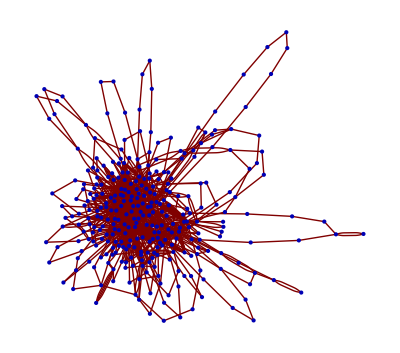

```mathematica
GraphPlot[oldPointers,VertexLabeling->Tooltip]
```

```mathematica
giveWordList[text_]:=Select[Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],{"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ",":"-> " ","/"->" "}]," "],#≠""&],!MemberQ[stopList,#]&]
```

```mathematica
giveTop[text_,size_]:=With[{pointers=Select[Tally[(#/.List->Rule)&/@ Partition[giveWordList[text],{2},1]],#[[2]]≥size&]},(*Give the 2-grams tallied that occur size or more than "size" times*)DeleteDuplicates[Flatten[Table[#[[1]]&/@Sort[Select[pointers,#[[1,1]]==pointers[[i,1,2]]&],#1[[2]]>#2[[2]]&],{i,1,Length[pointers]}]]]] (*return sorted pointers*)
```

```mathematica
words=StringJoin[(" "<>ExampleData[{"Text",#}]<>" ")&/@Select[#[[2]]&/@ExampleData["Text"],StringMatchQ[#,"*English"]&]];
```

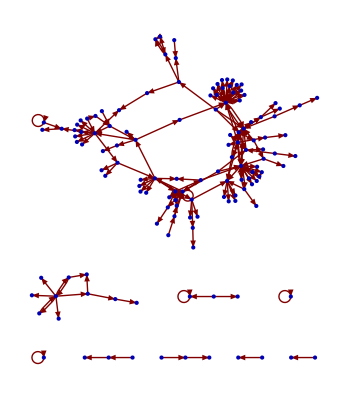

```mathematica
GraphPlot[giveTop[StringJoin[{ExampleData[{"Text","AliceInWonderland"}]," ",words}],9],DirectedEdges->True,VertexLabeling->Tooltip]
```